## Obliczenia numeryczne

```mathematica
Integrate[√(1+x^3),{x,0,1}]
```

Hypergeometric2F1[-1/2,1/3,4/3,-1]

```mathematica
NIntegrate[√(1+x^3),{x,0,1}]
```

1.11145

```mathematica
Solve[x^3==2,x,Reals]
NSolve[x^3==2,x,Reals]
```

{{x→Root1.26Root[-2+#1^3&,1]1.2599210498948732}}

{{x→1.25992}}

## Wykresy

```mathematica
Clear[g,x,y]
```

```mathematica
g[x_,y_]:=x^2+ y^2
```

```mathematica
Plot3D[g[x,y],{x,-1,1},{y,-1,1},PlotStyle->Blue]
```

-Graphics3D-

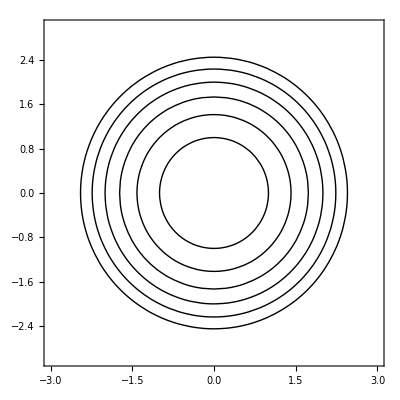

```mathematica
ContourPlot[g[x,y],{x,-3,3},{y,-3,3},Contours->{1,2,3,4,5,6},PlotLegends->Automatic, ColorFunction->"Rainbow",ContourShading->None]
```

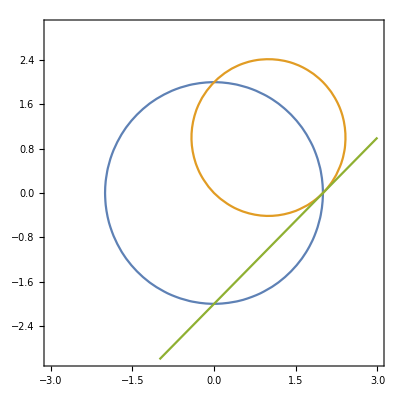

```mathematica
ContourPlot[{x^2+y^2==4,(x-1)^2+(y-1)^2==2,x-y==2},{x,-3,3},{y,-3,3},Axes->True]
```

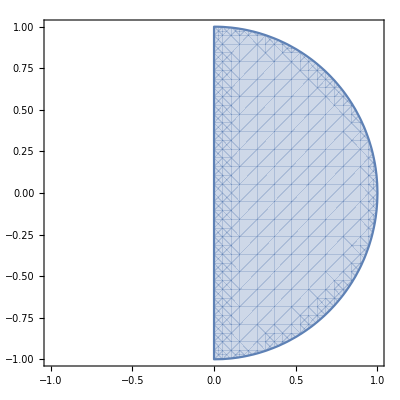

```mathematica
RegionPlot[g[x,y]<1&&x>0,{x,-1,1},{y,-1,1}]
```

```mathematica
Clear[g,v0,x,y]
```

```mathematica
g=9.81;
v0=10;
```

```mathematica
x[t_]:= v0 Cos[α]t
y[t_]:=  -1/2 g t^2+v0 Sin[α]t
```

```mathematica
Manipulate[ParametricPlot[{x[t], y[t]}/.α->angle ,{t,0,2v0 Sin[α]/g/.α->angle }, PlotRange->{{0,12},{0,10}}],{angle,0.001,π/2}]
```

```mathematica
ParametricPlot3D[{R0 Sin[ω t], R0 Cos[ω t], v t}/.{R0->1,ω->1,v->0.1},{t,0,100},PlotRange->{{-2,2},{-2,2},{0,10}}]
```

-Graphics3D-

```mathematica
r[ϕ_,ϵ_]:=(1+ϵ)/(1+ϵ Cos[ϕ])
```

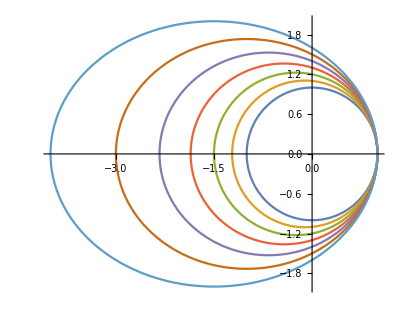

```mathematica
PolarPlot[Evaluate[Table[r[ϕ,e],{e,0,0.6,0.1}]],{ϕ,0,2 π},PlotRange->All]
```

## Macierze

```mathematica
M1={{a1,b1},{c1,d1}};
M2={{a2,b2},{c2,d2}};
```

```mathematica
MatrixForm[M1]
```

(a1 | b1
c1 | d1)

```mathematica
M2//MatrixForm
```

(a2 | b2
c2 | d2)

```mathematica
M1+M2//MatrixForm
```

(a1+a2 | b1+b2
c1+c2 | d1+d2)

```mathematica
M1 M2//MatrixForm (*To nie jest mnożnie macierzy!*)
```

(a1 a2 | b1 b2
c1 c2 | d1 d2)

```mathematica
Dot[M1,M2]//MatrixForm
```

(a1 a2+b1 c2 | a1 b2+b1 d2
a2 c1+c2 d1 | b2 c1+d1 d2)

```mathematica
M1.M2//MatrixForm
```

(a1 a2+b1 c2 | a1 b2+b1 d2
a2 c1+c2 d1 | b2 c1+d1 d2)

```mathematica
Transpose[M1]//MatrixForm
```

(a1 | c1
b1 | d1)

```mathematica
Inverse[M1]//MatrixForm
```

(d1/(-b1 c1+a1 d1) | -b1/(-b1 c1+a1 d1)
-c1/(-b1 c1+a1 d1) | a1/(-b1 c1+a1 d1))

```mathematica
Dot[Inverse[M1],M1]//MatrixForm
```

(-(b1 c1)/(-b1 c1+a1 d1)+(a1 d1)/(-b1 c1+a1 d1) | 0
0 | -(b1 c1)/(-b1 c1+a1 d1)+(a1 d1)/(-b1 c1+a1 d1))

```mathematica
Simplify[Dot[Inverse[M1],M1]]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Det[M1]
```

-b1 c1+a1 d1

```mathematica
Tr[M1]
```

a1+d1

## Dopasowywanie krzywych

```mathematica
data =Import[StringJoin[NotebookDirectory[],"oscillations.txt"],"Table"];
```

```mathematica
pointsplot = ListPlot[data,PlotRange->{{0,50},{-1.2,1.2}},Frame->True,GridLines->Automatic,FrameLabel->{"t [s]", "x [m]"},PlotMarkers->"+"]
```

-Graphics-

```mathematica
fit =NonlinearModelFit[data,Exp[-γ t]Cos[ω t],{γ, ω},t]
```

FittedModel[ⅇ^(-0.0449411 t) Cos[1.83988 t]]

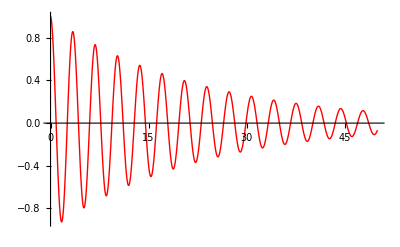

```mathematica
fitplot = Plot[Normal[fit],{t,0,50},PlotStyle->{Red,Thick}]
```

```mathematica
Show[pointsplot,fitplot]
```

-Graphics-

```mathematica
fit["BestFitParameters"]
```

{γ→0.0449411,ω→1.83988}

```mathematica
fit["ParameterErrors"]
```

{0.000979452,0.000982434}

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | 0.0449411 | 0.000979452 | 45.8839 | 4.41044×10^-77
ω | 1.83988 | 0.000982434 | 1872.78 | 8.95242×10^-266

```mathematica
res = Table[{data[[i,1]],fit["FitResiduals"][[i]]},{i,1,Length[data]}];
```

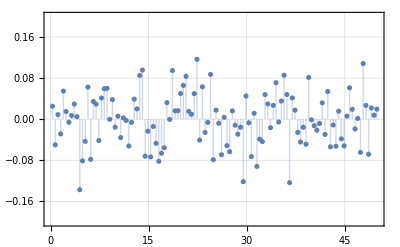

```mathematica
ListPlot[res,Filling->Axis,PlotRange->{{0,50},{-0.2,0.2}},Frame->True,GridLines->Automatic]
```